Задание переменных и функций:
x=1; F[x_]:=x^2;
Применение функции:
	 F@x                        (⇔F[x])
		x//F                    (⇔F[x])
		F@@{x,y,z}   (⇔F[x,y,z])
		F/@{x,y,z}   (⇔{F[x],F[y],F[z]})
Анонимные функции:
	#^2&     (⇔F[x_]:=x^2)

# Разбиения

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[2,10]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
Range[2,10,1/4]
Range[2,10,.25]
```

{2,9/4,5/2,11/4,3,13/4,7/2,15/4,4,17/4,9/2,19/4,5,21/4,11/2,23/4,6,25/4,13/2,27/4,7,29/4,15/2,31/4,8,33/4,17/2,35/4,9,37/4,19/2,39/4,10}

{2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.,5.25,5.5,5.75,6.,6.25,6.5,6.75,7.,7.25,7.5,7.75,8.,8.25,8.5,8.75,9.,9.25,9.5,9.75,10.}

```mathematica
Table[F[x],{x,2,10,.25}]
F/@Range[2,10,.25]
```

{F[2.],F[2.25],F[2.5],F[2.75],F[3.],F[3.25],F[3.5],F[3.75],F[4.],F[4.25],F[4.5],F[4.75],F[5.],F[5.25],F[5.5],F[5.75],F[6.],F[6.25],F[6.5],F[6.75],F[7.],F[7.25],F[7.5],F[7.75],F[8.],F[8.25],F[8.5],F[8.75],F[9.],F[9.25],F[9.5],F[9.75],F[10.]}

{F[2.],F[2.25],F[2.5],F[2.75],F[3.],F[3.25],F[3.5],F[3.75],F[4.],F[4.25],F[4.5],F[4.75],F[5.],F[5.25],F[5.5],F[5.75],F[6.],F[6.25],F[6.5],F[6.75],F[7.],F[7.25],F[7.5],F[7.75],F[8.],F[8.25],F[8.5],F[8.75],F[9.],F[9.25],F[9.5],F[9.75],F[10.]}

```mathematica
Sin/@Range[10]//N
```

{0.841471,0.909297,0.14112,-0.756802,-0.958924,-0.279415,0.656987,0.989358,0.412118,-0.544021}

Range[]
Table[]
Subdivide[]
Partition[]

*Эффективный аналог цикла For[]:

```mathematica
F/@G/@H/@Range[2,5]
```

{F[G[H[2]]],F[G[H[3]]],F[G[H[4]]],F[G[H[5]]]}

```mathematica
For[i=2,i≤5,i++,
h=H[i];
g=G[h];
f=F[g];
Print[f]
];
```

F[G[H[2]]]

F[G[H[3]]]

F[G[H[4]]]

F[G[H[5]]]

# Графики

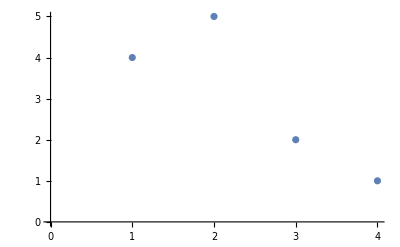

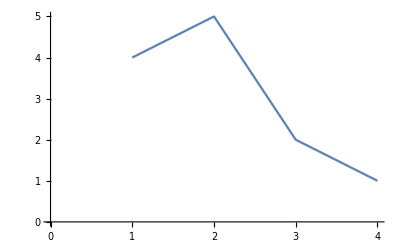

```mathematica
ListPlot[{4,5,2,1}]
ListLinePlot[{4,5,2,1}]
```

График функции на заданном интервале

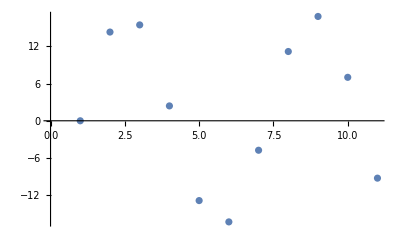

```mathematica
17Sin/@Range[0,10]//ListPlot
```

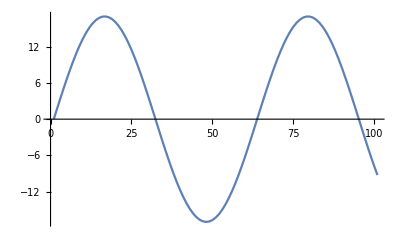

```mathematica
17Sin/@Range[0,10,.1]//ListLinePlot
```

График с явными значениями аргумента

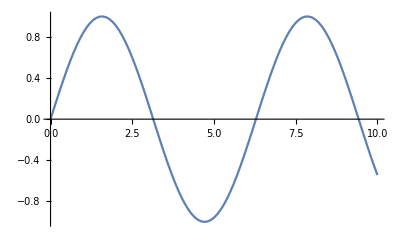

-Graphics-

```mathematica
Table[{x,Sin[x]},{x,0,10,.1}]//ListLinePlot
{#,Sin[#]}&/@Range[0,10,.1]//ListLinePlot
```

График нескольких списков

{Cos[5],Cos[10],Cos[15],Cos[20],Cos[25],Cos[30]}

{Sin[5],Sin[10],Sin[15],Sin[20],Sin[25],Sin[30]}

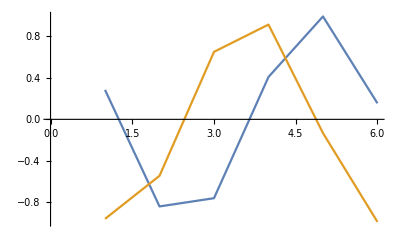

```mathematica
tab1=Cos/@(5Range[6])
tab2=Sin/@(5Range[6])
ListLinePlot[{tab1,tab2}]
```

Транспонирование многомерных списков

```mathematica
{tab1,tab2}
{tab1,tab2}ᵀ
```

{{Cos[5],Cos[10],Cos[15],Cos[20],Cos[25],Cos[30]},{Sin[5],Sin[10],Sin[15],Sin[20],Sin[25],Sin[30]}}

{{Cos[5],Sin[5]},{Cos[10],Sin[10]},{Cos[15],Sin[15]},{Cos[20],Sin[20]},{Cos[25],Sin[25]},{Cos[30],Sin[30]}}

```mathematica
{tab1,tab2}//MatrixForm
{tab1,tab2}ᵀ//MatrixForm
```

(Cos[5] | Cos[10] | Cos[15] | Cos[20] | Cos[25] | Cos[30]
Sin[5] | Sin[10] | Sin[15] | Sin[20] | Sin[25] | Sin[30])

(Cos[5] | Sin[5]
Cos[10] | Sin[10]
Cos[15] | Sin[15]
Cos[20] | Sin[20]
Cos[25] | Sin[25]
Cos[30] | Sin[30])

График списка пар = параметрический график списка

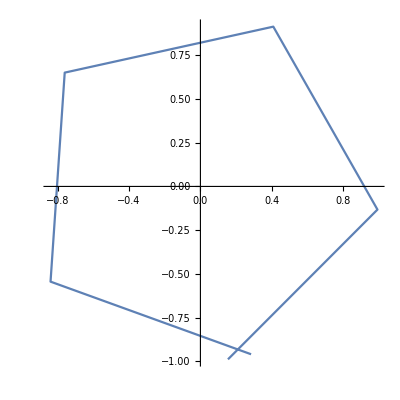

```mathematica
ListLinePlot[{tab1,tab2}ᵀ,AspectRatio->1]
```

Transpose[] (ᵀ= tr)

График с автоматическим разбиением

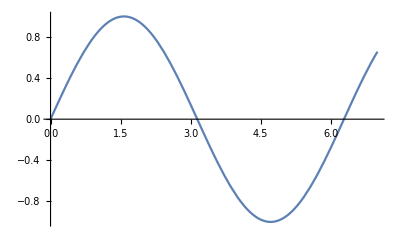

```mathematica
Plot[Sin[x],{x,0,7}]
```

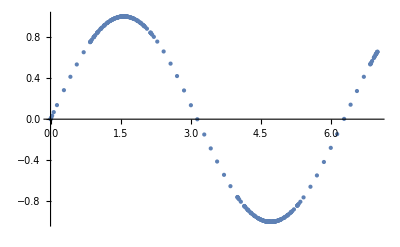

```mathematica
Plot[Sin[x],{x,0,7}]/.Line->Point
```

График нескольких функций

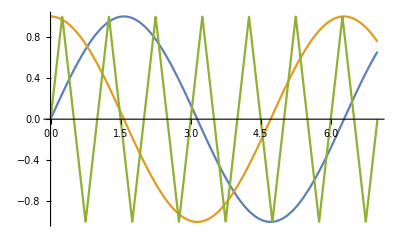

```mathematica
Plot[{Sin[x],Cos[x],TriangleWave[x]},{x,0,7}]
```

Параметрические графики с автоматическим разбиением

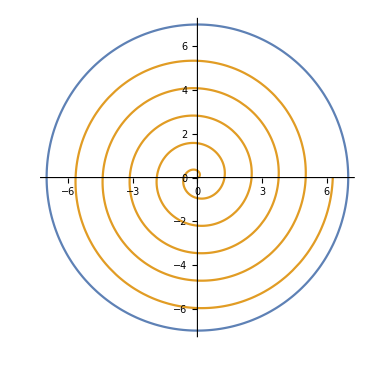

```mathematica
ParametricPlot[{7{Cos[φ],Sin[φ]},φ{Cos[5φ],Sin[5φ]}},{φ,0,2π}]
```

Обобщённая форма

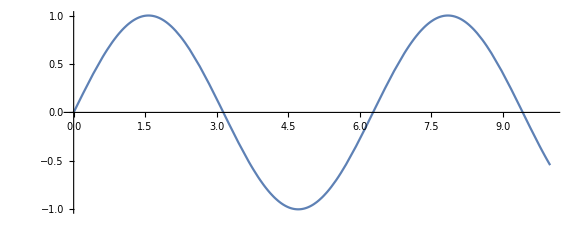

```mathematica
ParametricPlot[{φ1,Sin[φ1]},{φ1,0,10}]
```

Plot[]
ListPlot[]
ParametricPlot[]
PolarPlot[]
LogLogPlot[]
ContourPlot[]
RegionPlot[]
…
Plot3D[]
…

Объединение графиков

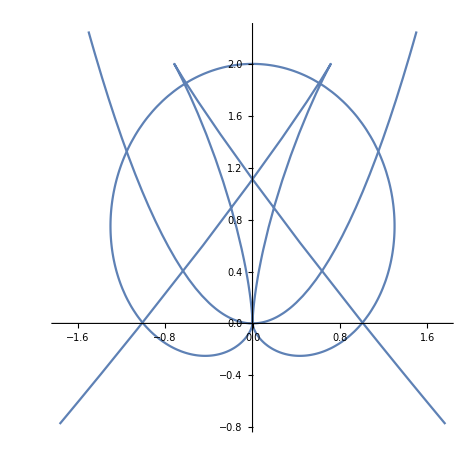

```mathematica
plot1=Plot[x^2,{x,-1.5,1.5}];
plot2=ParametricPlot[{{20(-t^3+3 t^5), 10 t^2(2-5 t^2)}},{t,-.66,.66}];
plot3=PolarPlot[1+Sin[φ],{φ,0,2π}];

Show[{
plot1,
plot2,
plot3
},PlotRange->All,AspectRatio->1]
```

# Параметры графиков

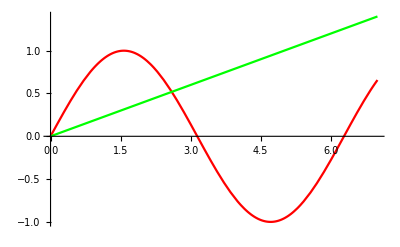

```mathematica
Plot[{Sin[x],x/5},{x,0,7},PlotStyle->{Red,Green}]
```

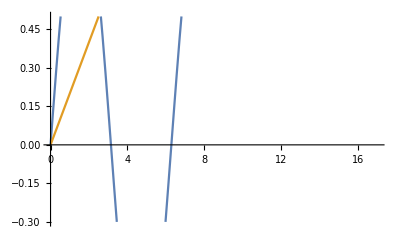

```mathematica
Plot[{Sin[x],x/5},{x,0,7},PlotRange->{{0,17},{-.3,.5}}]
```

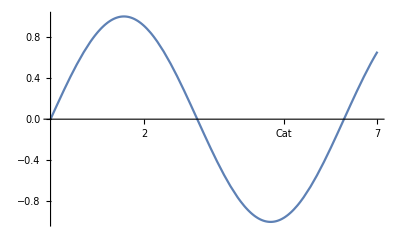

```mathematica
Plot[Sin[x],{x,0,7},Ticks->{{2,{5,"Cat"},7},Automatic}]
```

Параметры численных методов

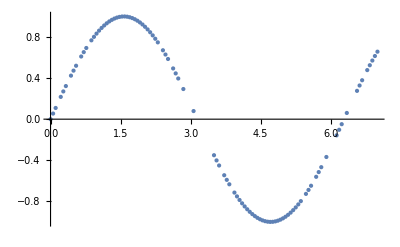

```mathematica
Plot[Sin[x],{x,0,7},PlotPoints->2,MaxRecursion->7]/.Line->Point
```

PlotPoints→
MaxRecursion→

Полный список настроек в справке функции Plot[]

# Динамические выражения

```mathematica
Pic[T_]:=ParametricPlot[φ{Sin[φ],Cos[φ]-Sin[2φ]},{φ,0,T},PlotRange->15{{-1,1},{-1,1}}];
Manipulate[Pic[T],{T,1,15}]
```